# multi-level atom master equation - network exp. calculations

P. Huft

See my multi_level_atom_master_eq.nb for low-level testing and reproduction of Mark’s examples.

For solving time dynamics of a density matrix describing an individual multi-level atom, with a Hamiltonian accounting for interaction with multiple classical light fields, and Linblad terms to account for spontaneous emission.

See Mark’s atomic notes, Eqs. 12.18 (the expression for the general density matrix equation matrix elements for N levels and M fields, right before the Optical pumping of Holmium section). Note that the second two sums in the first line of 12.18b should be constrained such that j!=l in the first one and k!=j in the second-- this is because the decay of coherences does not depend on populations. The second sum needs to be split so that the first index of rho is greater than the second. This means that in one of the sums the complex conjugate of the coherence will have to be used since we are dropping redundant coherences rho_{k,j>k}. This last point was addressed in the version of MEqs in setup, but not in the version for debugging with two and four level atoms (the associated errors do not manifest themselves there though).

## setup - run first

```mathematica
constsdir="..\\constants\\";
imagedir=FileNameJoin[{NotebookDirectory[],"\\images\\"}];
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],constsdir}]];
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
<<"rbconsts.m"
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
imag[z_]:=(z-conj[z])/2;
δsym[a_,b_]:=KroneckerDelta[SymbolName[a],SymbolName[b]];
TrueFalse[x_]:=If[x==0,False,True];(*python-like numeric True/False function*)
OoM[x_]:=Floor[Log10[Abs[x]+10^-9]+0.5];
DropHiOsc[detuning_,oom_]:=If[OoM[detuning/(2π)]<oom,1,0](*returns 0 (1) if O[detuning/(2π)] is more (less) than a specified order of magnitude. can by used as a multiplier to drop potentially highly-oscillatory terms*)
OrbAngLetter[L_]:=Switch[L,0,"S",1,"P",2,"D",3,"F"];
KetForm[state_]:=state[[1]] Subscript[OrbAngLetter[state[[2]]], state[[3]]//Rationalize],state[[4]],state[[5]];

(*the double letters denote the upper state quantum numbers*)
E1MatElemHF[{J_,F_,mF_},{JJ_,FF_,mFF_},q_]:=(-1)^(1+i+JJ+F)√(2F+1)SixJSymbol[{J,i,F},{FF,1,JJ}]ClebschGordan[{F,mF},{1,q},{FF,mFF}];
δ[a_,b_]:=KroneckerDelta[a,b];
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 14],ImageSize->Medium];
SetOptions[PolarPlot,PolarAxes->True,PolarGridLines->Automatic,PolarTicks->{Drop[Table[i,{i,0,2 Pi,Pi/4}],-1],Automatic},LabelStyle->Directive[Black, 15],ImageSize->Medium];
(*some units*)
ppm = 10^-6;
GHz=10^9;
MHz=10^6;
(*the population and coherence indices for a ρ vector ordered the same as the equations generated by the MEqs used in the two- and four-level examples*)
Indices[dim_]:=Module[{i=Floor[dim(dim+1)/2+0.5],m=Floor[dim(dim+1)/2+0.5],j=2,pops={},cohs={}},
While[i>0,
AppendTo[pops,i];
i-=j;
j++;
];
{Reverse[pops],Complement[Range[dim(dim+1)/2],pops]}
]
Clear[MEqs]
MEqs[stateList_,fieldAmplitudes_,detunings_,dipoleMatrixElement_,decayRate_,dropFastOoM_,excludeIndices_:{}]:=Module[{drop,states=stateList,Ep=fieldAmplitudes,d=dipoleMatrixElement,γ=decayRate,Δ=detunings,l=1,k=1,dim=1,dimE=1,populationRHS, coherenceRHS,populationDriving,populationDecay,coherenceDriving,coherenceDecay,RHS=0,Eqs={},HO,Ex},
(*Builds the density matrix master equation in Linblad form for each element Subscript[ρ, k,l] with k>l and k increasing in order of energy. The coherence terms are actually ρ̃=ρⅇ^-ⅈωt.

--- Params ---
fieldAmplitudes, detunings, dipoleMatrixElement, and decayRate: functions that depend on state indices j,k and field indices p to return the appropriate quantity. See usage below.

dropFastOoM: an order of magnitude of the detuning (in the chosen energy units of the states and fields, e.g. GHz).

excludeIndices: a list of indices {k,l} for which equations for Subscript[ρ, k,l] and dependence on Subscript[ρ, k,l] in other eqs will be dropped
*)
dim = Length[states];
dimE=Length[Ep];
(*--multipliers for systematically dropping terms--*)
Table[Subscript[HO, p,i,j]=DropHiOsc[Δ[p,i,j],dropFastOoM],{p,Range[dimE]},{i,Range[dim]},{j,Range[dim]}];(*for removing highly oscillatory (far off-resonant) terms*)
Table[Subscript[Ex, k,l]=Subscript[Ex, l,k]=Boole[!MemberQ[excludeIndices,{k,l}]],{l,Range[dim]},{k,Range[l,dim]}];(*for removing the equations for and terms with Subscript[ρ, k,l] if {k,l} ∈ excludeIndices*)

(*--Generate the population eqs--*)
For[k=1,k<dim+1,k++,
RHS=
-Sum[γ[j,k]Subscript[ρ, k,k][t],{j,Range[1,k-1]}]+Sum[γ[k,j]Subscript[ρ, j,j][t],{j,Range[k+1,dim]}]
-ⅈ/(2ℏ)(Sum[(-Ep[[p]]d[k,j,p]Subscript[ρ, k,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,k,p]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,k,j]t])Subscript[HO, p,k,j] Subscript[Ex, k,j],{p,Range[dimE]},{j,Range[1,k-1]}]
+Sum[(Ep[[p]]d[j,k,p]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,k]t]-Ep[[p]]*d[k,j,p]Subscript[ρ, j,k][t]Exp[ⅈ Δ[p,j,k]t])Subscript[HO, p,j,k] Subscript[Ex, j,k],{p,Range[dimE]},{j,Range[k+1,dim]}]);
AppendTo[Eqs,D[Subscript[ρ, k,k][t],t]==RHS];
];
(*--Generate the coherence eqs--*)
For[l=1,l<dim+1,l++,
For[k=l+1,k<dim+1,k++,
If[!MemberQ[excludeIndices,{k,l}],
RHS=1/2(-(Sum[γ[j,k],{j,Range[1,k-1]}]+Sum[γ[j,l],{j,Range[1,l-1]}])Subscript[ρ, k,l][t]
+Sum[γ[k,j]Subscript[ρ, j,l][t](1-δ[j,l])Subscript[Ex, j,l],{j,Range[k+1,dim]}]+Sum[γ[l,j]Subscript[ρ, k,j][t](1-δ[k,j])Subscript[Ex, k,j],{j,Range[l+1,k-1]}]+Sum[γ[l,j]Subscript[ρ, j,k][t]*(1-δ[k,j])Subscript[Ex, j,k],{j,Range[k+1,dim]}]
-ⅈ/ℏ(Sum[-Ep[[p]]d[k,j,p]Subscript[ρ, l,j][t]*Exp[-ⅈ Δ[p,k,j]t] Subscript[HO, p,k,j] Subscript[Ex, l,j]+Ep[[p]]*d[j,l,p]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,l,j]t] Subscript[HO, p,l,j] Subscript[Ex, k,j],{p,Range[dimE]},{j,Range[1,l-1]}]
+Sum[Ep[[p]](d[j,l,p]Subscript[ρ, k,j][t]Exp[-ⅈ Δ[p,j,l]t] Subscript[HO, p,j,l] Subscript[Ex, k,j]-d[k,j,p]Subscript[ρ, j,l][t]Exp[-ⅈ Δ[p,k,j]t] Subscript[HO, p,k,j] Subscript[Ex, j,l]),{p,Range[dimE]},{j,Range[l,k-1]}]
+Sum[Ep[[p]]d[j,l,p]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,l]t] Subscript[HO, p,j,l] Subscript[Ex, j,k]-Ep[[p]]*d[k,j,p]Subscript[ρ, j,l][t]Exp[ⅈ Δ[p,j,k]t] Subscript[HO, p,j,k] Subscript[Ex, j,l],{p,Range[dimE]},{j,Range[k,dim]}]));
AppendTo[Eqs,D[Subscript[ρ, k,l][t],t]==RHS];
];
];
];

Eqs
]
```

## Two-level atom calculations

Test of simulated Rabi oscillations and relaxation.

```mathematica
Δ=2π;
states={{gg,0},{ee,Δ}};(*state labels and indices*)
{level,energies}=Transpose@states;

Γ= 0.1;(*the upper state lifetime*)
(*tπ=0.6*(2π)/Γ*);(*we want π time much less than the lifetime*)
Ω0=2π (π/tπ);(*Rabi frequency in terms of pi time*)
(*pulseShape=HeavisideTheta[tπ-t];*)
pulseShape=1;
(*lists of field amplitudes and ang. freq*)
Efields={{Ω0*pulseShape,Ω0*pulseShape}};(*by setting the matrix element d=1, Efield alone determines Rabi frequency*)
{Ep,ωp} = Transpose@Efields;
dimE=Length[Ep];
(*things that depend on a pair of state indices j and k:*)
d[j_,k_]:=(1-δ[j,k]);(*trivial*)
γ[j_,k_]:=(1-δ[j,k])Γ;
Δ[p_,k_,j_]:=ωp[[p]]-(energies[[k]]-energies[[j]]);
Clear[Eqs];
Eqs={};
For[l=1,l<dim+1,l++,
For[k=l,k<dim+1,k++,
RHS=
δ[k,l](-Sum[γ[j,k]Subscript[ρ, k,k][t],{j,Range[1,k-1]}]+Sum[γ[k,j]Subscript[ρ, j,j][t],{j,Range[k+1,dim]}]
-ⅈ/2(Sum[-Ep[[p]]d[k,j]Subscript[ρ, k,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,k]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,k,j]t],{p,Range[dimE]},{j,Range[1,k-1]}]
+Sum[Ep[[p]]d[j,k]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,k]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,k][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k+1,dim]}]))
+1/2(1-δ[k,l])(-(Sum[γ[j,k],{j,Range[1,k-1]}]+Sum[γ[j,l],{j,Range[1,l-1]}])Subscript[ρ, k,l][t]
+Sum[γ[k,j]Subscript[ρ, j,l][t]δ[j,l],{j,Range[k+1,dim]}]+Sum[γ[l,j]Subscript[ρ, k,j][t]δ[j,l],{j,Range[l+1,dim]}]
-ⅈ(Sum[-Ep[[p]]d[k,j]Subscript[ρ, l,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,l]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,l,j]t],{p,Range[dimE]},{j,Range[1,l-1]}]
+Sum[Ep[[p]](d[j,l]Subscript[ρ, k,j][t]Exp[-ⅈ Δ[p,j,l]t]-d[k,j]Subscript[ρ, j,l][t]Exp[-ⅈ Δ[p,k,j]t]),{p,Range[dimE]},{j,Range[l,k-1]}]
+Sum[Ep[[p]]d[j,l]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,l]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,l][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k,dim]}]))//FullSimplify;
AppendTo[Eqs,D[Subscript[ρ, k,l][t],t]==RHS];
Print[TraditionalForm[D[Subscript[ρ, k,l][t],t]==RHS]];
]
]
tmax=4/Γ;
rho={Subscript[ρ, 1,1][t],Subscript[ρ, 2,1][t],Subscript[ρ, 2,2][t]};
rho0={1,0,0};
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax}]];
Print["Time to run sim: ",time];
```

ρ_(1,1)'(t)==(0.-164493. ⅈ) ⅇ^((0.-328986. ⅈ) t) Conjugate[ρ_(2,1)(t)]+(0.+164493. ⅈ) ⅇ^((0.+328986. ⅈ) t) ρ_(2,1)(t)+0.1 ρ_(2,2)(t)

ρ_(2,1)'(t)==-0.05 ρ_(2,1)(t)+(0.-164493. ⅈ) ⅇ^((0.-328986. ⅈ) t) (1. Conjugate[ρ_(2,2)(t)]-1. ρ_(1,1)(t))

ρ_(2,2)'(t)==(0.+164493. ⅈ) ⅇ^((0.-328986. ⅈ) t) Conjugate[ρ_(2,1)(t)]-(0.+164493. ⅈ) ⅇ^((0.+328986. ⅈ) t) ρ_(2,1)(t)-0.1 ρ_(2,2)(t)

$Aborted

Time to run sim: 0.

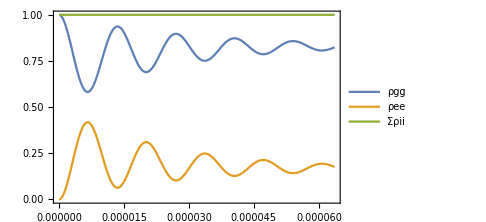

```mathematica
tplotmax=tmax;
plt ={};
labels={"ρgg","ρee","Σρii"};
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,soln[[i,2]]]
];
populations={1,3};
AppendTo[plt,Total[soln[[populations,2]]]];
AppendTo[populations,-1];
Show[Plot[Evaluate[plt[[populations]]], {t, 0, tplotmax},PlotRange->All,PlotLegends->labels],Plot[Evaluate[pulseShape[t]], {t, 0, tplotmax},PlotRange->All,PlotLegends->"Ω(t)/Ω_0",PlotStyle->Black]]
```

```mathematica
Ω0/(2π)
Γ/(2π)
```

3141.59

1

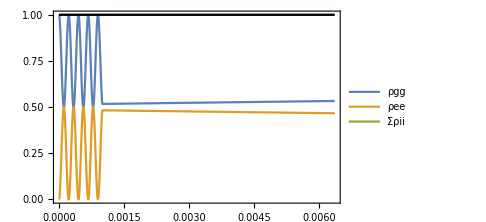

```mathematica
tplotmax=tmax/100;
plt ={};
labels={"ρgg","ρee","Σρii"};
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,soln[[i,2]]]
];
populations={1,3};
AppendTo[plt,Total[soln[[populations,2]]]];
AppendTo[populations,-1];
Show[Plot[Evaluate[plt[[populations]]], {t, 0, tplotmax},PlotRange->All,PlotLegends->labels],Plot[Evaluate[Ω[t]/Ω0], {t, 0, tplotmax},PlotRange->All,PlotLegends->"Ω(t)/Ω_0",PlotStyle->Black]]
```

```mathematica
Ω[t]/.
```

π HeavisideTheta[1-t]

## Three-level STIRAP

Test of simulated Rabi oscillations and relaxation.

```mathematica
Δ=2π;
states={{gg,0},{ee,Δ}};(*state labels and indices*)
{level,energies}=Transpose@states;

Γ= 0.1;(*the upper state lifetime*)
(*tπ=0.6*(2π)/Γ*);(*we want π time much less than the lifetime*)
Ω0=2π (π/tπ);(*Rabi frequency in terms of pi time*)
(*pulseShape=HeavisideTheta[tπ-t];*)
pulseShape=1;
(*lists of field amplitudes and ang. freq*)
Efields={{Ω0*pulseShape,Ω0*pulseShape}};(*by setting the matrix element d=1, Efield alone determines Rabi frequency*)
{Ep,ωp} = Transpose@Efields;
dimE=Length[Ep];
(*things that depend on a pair of state indices j and k:*)
d[j_,k_]:=(1-δ[j,k]);(*trivial*)
γ[j_,k_]:=(1-δ[j,k])Γ;
Δ[p_,k_,j_]:=ωp[[p]]-(energies[[k]]-energies[[j]]);
Clear[Eqs];
Eqs={};
For[l=1,l<dim+1,l++,
For[k=l,k<dim+1,k++,
RHS=
δ[k,l](-Sum[γ[j,k]Subscript[ρ, k,k][t],{j,Range[1,k-1]}]+Sum[γ[k,j]Subscript[ρ, j,j][t],{j,Range[k+1,dim]}]
-ⅈ/2(Sum[-Ep[[p]]d[k,j]Subscript[ρ, k,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,k]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,k,j]t],{p,Range[dimE]},{j,Range[1,k-1]}]
+Sum[Ep[[p]]d[j,k]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,k]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,k][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k+1,dim]}]))
+1/2(1-δ[k,l])(-(Sum[γ[j,k],{j,Range[1,k-1]}]+Sum[γ[j,l],{j,Range[1,l-1]}])Subscript[ρ, k,l][t]
+Sum[γ[k,j]Subscript[ρ, j,l][t]δ[j,l],{j,Range[k+1,dim]}]+Sum[γ[l,j]Subscript[ρ, k,j][t]δ[j,l],{j,Range[l+1,dim]}]
-ⅈ(Sum[-Ep[[p]]d[k,j]Subscript[ρ, l,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,l]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,l,j]t],{p,Range[dimE]},{j,Range[1,l-1]}]
+Sum[Ep[[p]](d[j,l]Subscript[ρ, k,j][t]Exp[-ⅈ Δ[p,j,l]t]-d[k,j]Subscript[ρ, j,l][t]Exp[-ⅈ Δ[p,k,j]t]),{p,Range[dimE]},{j,Range[l,k-1]}]
+Sum[Ep[[p]]d[j,l]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,l]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,l][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k,dim]}]))//FullSimplify;
AppendTo[Eqs,D[Subscript[ρ, k,l][t],t]==RHS];
Print[TraditionalForm[D[Subscript[ρ, k,l][t],t]==RHS]];
]
]
tmax=4/Γ;
rho={Subscript[ρ, 1,1][t],Subscript[ρ, 2,1][t],Subscript[ρ, 2,2][t]};
rho0={1,0,0};
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax}]];
Print["Time to run sim: ",time];
```

ρ_(1,1)'(t)==(0.-164493. ⅈ) ⅇ^((0.-328986. ⅈ) t) Conjugate[ρ_(2,1)(t)]+(0.+164493. ⅈ) ⅇ^((0.+328986. ⅈ) t) ρ_(2,1)(t)+0.1 ρ_(2,2)(t)

ρ_(2,1)'(t)==-0.05 ρ_(2,1)(t)+(0.-164493. ⅈ) ⅇ^((0.-328986. ⅈ) t) (1. Conjugate[ρ_(2,2)(t)]-1. ρ_(1,1)(t))

ρ_(2,2)'(t)==(0.+164493. ⅈ) ⅇ^((0.-328986. ⅈ) t) Conjugate[ρ_(2,1)(t)]-(0.+164493. ⅈ) ⅇ^((0.+328986. ⅈ) t) ρ_(2,1)(t)-0.1 ρ_(2,2)(t)

$Aborted

Time to run sim: 0.

```mathematica
tplotmax=tmax;
plt ={};
labels={"ρgg","ρee","Σρii"};
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,soln[[i,2]]]
];
populations={1,3};
AppendTo[plt,Total[soln[[populations,2]]]];
AppendTo[populations,-1];
Show[Plot[Evaluate[plt[[populations]]], {t, 0, tplotmax},PlotRange->All,PlotLegends->labels],Plot[Evaluate[pulseShape[t]], {t, 0, tplotmax},PlotRange->All,PlotLegends->"Ω(t)/Ω_0",PlotStyle->Black]]
```

-Graphics-

```mathematica
Ω0/(2π)
Γ/(2π)
```

3141.59

1

```mathematica
tplotmax=tmax/100;
plt ={};
labels={"ρgg","ρee","Σρii"};
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,soln[[i,2]]]
];
populations={1,3};
AppendTo[plt,Total[soln[[populations,2]]]];
AppendTo[populations,-1];
Show[Plot[Evaluate[plt[[populations]]], {t, 0, tplotmax},PlotRange->All,PlotLegends->labels],Plot[Evaluate[Ω[t]/Ω0], {t, 0, tplotmax},PlotRange->All,PlotLegends->"Ω(t)/Ω_0",PlotStyle->Black]]
```

-Graphics-

```mathematica
Ω[t]/.
```

π HeavisideTheta[1-t]

## “Realistic” atom with hyperfine states

Run the 4-level cell above define the equation generator module, MEqs. Now that we are dealing with “realistic” atoms we need to choose some useful units of energy. I use GHz.
Examples to try with a Rb atom in a constrained space to make the test easy to debug:
[] Driving Rabi oscillations between 5S1/2 F=1 and 5P3/2 F=0 states with one field whose linear polarization is angled to equalize the three transition rates.
[] Raman on D2 line on a pair of transitions 5S1/2,F=1,m=1,5S1/2,F=2,m=2 to  5P3/2,F=2,m=2 with linear light quasi-resonant from F=2->F=2 and RH light quasi-resonant on F=1->F=2.  Include the 5S1/2,F=2,m=1 state to which population will eventually end up.

## ^87 Rb - D2 damped Rabi oscillations, F=1,m=0->F’=0,m=0

With linear polarization aligned to the quantization axis, and population initially in F=1,m=0, the population will gradually be pumped to the m=+/-1 dark states.

```mathematica
(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)

Fglist={1}(*Range[Abs[INuc-1/2],INuc+1/2]*);(*list of ground state hyperfine levels F*)
Fe1list=Fglist(*Range[Abs[INuc-1/2],INuc+1/2]*);
Fe2list={0};(*Range[Abs[INuc-3/2],INuc+3/2]*);
FivePThreeHalves=Flatten[Table[Table[{5,1,3/2,f,mf},{mf,Range[-f,f]}],{f,Fe2list}(*Range[Abs[INuc-3/2],INuc+3/2]}*)],1];
FivePOneHalf=Flatten[Table[Table[{5,1,1/2,f,mf},{mf,Range[-f,f]}],{f,Fe1list}],1];
FiveSOneHalf=Flatten[Table[Table[{5,0,1/2,f,mf},{mf,Range[-f,f]}],{f,Fglist}],1];
states=Join[FiveSOneHalf,FivePThreeHalves];
{n,L,J,F,mF}=Transpose@states;
"Total number of states:"
dim=Length[states]

(*the energy of each state*)
ω=Table[2π Rb87fGHz[states[[i]][[;;4]]],{i,Range[dim]}];

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Ε1,Ε2,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);

det =2π*10^-9;(*detuning. must be finite, but can be arbitrarily small*)
Efields={{Ε1,2π(Rb87fGHz[{5,1,3/2,0}]-Rb87fGHz[{5,0,1/2,1}]-det),0,0}(*,{Ε2,2π(Rb87fGHz[{5,1,3/2,2}]-Rb87fGHz[{5,0,1/2,2}])-det, 0,0}*)};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

dRotated[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, d[m,n,p]=d[n,m,p].*)
Quiet[(Sum[WignerD[{F[[k]],mF[[k]],mFk},θ[[p]]]WignerD[{F[[j]],mFj,mF[[j]]},θ[[p]]]ClebschGordan[{F[[j]],mFj},{1,q[[p]]},{F[[k]],mFk}],{mFk,Range[-F[[k]],F[[k]]]},{mFj,Range[-F[[j]],F[[j]]]}])(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]E1FineReduced[j,k]]
]

γE1[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},γD1,{{5,0,1/2},{5,1,3/2}},γD2,_,0];(*get hardcoded D1 or D2 line natural linewidth.*)

(*branching factor from an upper state k to j*)
b[{J_,F_,mF_},{JJ_,FF_,mFF_}]:=Quiet[(2F+1)SixJSymbol[{J,INuc,F},{FF,1,JJ}]^2 ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}]^2];

(*pre-evaluate b values*)
Table[Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]=b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}],{j,Range[dim]},{k,Range[j,dim]}];

(*decay from state k to j*)
γ[j_,k_]:=γE1[j,k](Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]/Total[Flatten[Table[Subscript[bb, J[[1]],Fg,mFg,J[[k]],F[[k]],mF[[k]]],{Fg,Fglist},{mFg,Range[-Fg,Fg]}],1]]);
(*γ[j_,k_]:=γE1[j,k](b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}]/Total[Flatten[Table[Table[b[{J[[1]],Fg,mFg},{J[[k]],F[[k]],mF[[k]]}],{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]);*)

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);

(*pre-evaluate γ, d, and Δ values which we can "look up" by index*)
Table[γlookup[j,k]=γ[j,k],{j,Range[dim]},{k,Range[j,dim]}];
Table[dlookup[j,k,p]=dRotated[j,k,p],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];
Table[Δlookup[p,k,j]=Δ[p,k,j],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];

(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[10]+1;(*GHz*)

(*equations to exclude for an approximate but much faster result*)
gExclude=Flatten[Table[{k,j},{j,Range[3]},{k,Range[j+1,3]}],1];(*coherences betweeen  5S1/2 hyperfine states*)
eExclude=Flatten[Table[{k,j},{j,Range[4,6]},{k,Range[j+1,6]}],1];(*coherences betweeen  5P1/2 hyperfine states*)
exclude=Join[gExclude,eExclude];

Eqs = MEqs[states,Ep,Δlookup,dlookup,γlookup,drop,exclude];(*generate the differential equations*)
"Number of equations"
Eqs//Length
"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]
```

Total number of states:

4

Number of equations

7

The equations to be solved:

ρ_(1,1)'(t)==1/3 γD2 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(2,2)'(t)==(0.+1.37464×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(4,2)(t)]-(0.+1.37464×10^33 ⅈ) dD2 ⅇ^((0.-3.95812×10^-8 ⅈ) t) Conjugate[Ε1] ρ_(4,2)(t)+1/3 γD2 ρ_(4,4)(t)

ρ_(3,3)'(t)==1/3 γD2 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(4,4)'(t)==(0.-1.37464×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(4,2)(t)]+(0.+1.37464×10^33 ⅈ) dD2 ⅇ^((0.-3.95812×10^-8 ⅈ) t) Conjugate[Ε1] ρ_(4,2)(t)-γD2 ρ_(4,4)(t)

ρ_(4,1)'(t)==-1/2 γD2 ρ_(4,1)(t)+(0.+0. ⅈ)

ρ_(4,2)'(t)==(0.+1.37464×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(4,4)(t)]-(0.+1.37464×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) ρ_(2,2)(t)-1/2 γD2 ρ_(4,2)(t)

ρ_(4,3)'(t)==-1/2 γD2 ρ_(4,3)(t)+(0.+0. ⅈ)

```mathematica
(*--define numerical constants--*)
dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Ε1=Ε2=10√(2/(c ϵ0)IsatD2SI) /GHz;

(*--setup for the numerical solver--*)

(*the list of populations and coherences we're including, in the same order as in Eqs*)
rho=Join[Table[Subscript[ρ, k,k][t],{k,Range[dim]}],Complement[Flatten[Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l+1,dim}],1],Array[Subscript[ρ, exclude[[#,1]],exclude[[#,2]]][t]&,Length[exclude]]]];
rho0=Array[0&,Length[rho]];
(*rho0[[{1,2,3}]]=1/3;*)
rho0[[2]]=1;
Ω1=Ε1 d[2,4,1]/ℏ;
(*Ω2=Ε2 d[8,17,2]/ℏ;*)
Ωeff=Abs[Ω1] ;
Print["Effective rabi frequency = 2π*",Ωeff/(2π) GHz/MHz," MHz"]
tmax=10*2π/Ωeff;
```

Effective rabi frequency = 2π*21.5398 MHz

Time to run sim: 0.

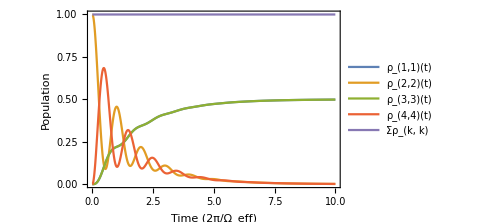

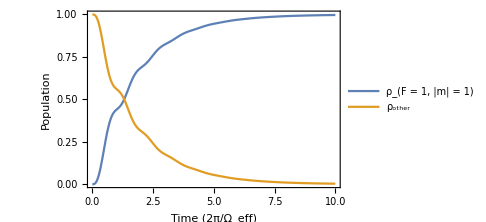

```mathematica
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic]](*,MaxStepFraction->0.001]]*);
Print["Time to run sim: ",time];
labels=rho[[;;dim]];
AppendTo[labels,"Σρ_(k, k)"];
lines=Re[(rho/.soln)[[;;dim]]];
AppendTo[lines,Total[(rho/.soln)[[;;dim]]]];
(*Plot[Evaluate[lines], {t, 0,tmax },PlotRange->All,PlotLegends->labels]*)
Plot[Evaluate[lines/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->labels,FrameLabel->{"Time (2π/Ω_eff)","Population"}]
Plot[Evaluate[{Total[lines[[{1,3}]]],Total[lines[[{2,4}]]]}/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->{"ρ_(F = 1, |m| = 1)","ρ_other"},FrameLabel->{"Time (2π/Ω_eff)","Population"}]
```

## ^87 Rb - D2 excitation with a short Gaussian pulse, F=1,m=0->F’=0,m=0

With linear polarization aligned to the quantization axis, and population initially in F=1,m=0, the population will gradually be pumped to the m=+/-1 dark states.

```mathematica
(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)

Fglist={1}(*Range[Abs[INuc-1/2],INuc+1/2]*);(*list of ground state hyperfine levels F*)
Fe1list=Fglist(*Range[Abs[INuc-1/2],INuc+1/2]*);
Fe2list={0};(*Range[Abs[INuc-3/2],INuc+3/2]*);
FivePThreeHalves=Flatten[Table[Table[{5,1,3/2,f,mf},{mf,Range[-f,f]}],{f,Fe2list}(*Range[Abs[INuc-3/2],INuc+3/2]}*)],1];
FivePOneHalf=Flatten[Table[Table[{5,1,1/2,f,mf},{mf,Range[-f,f]}],{f,Fe1list}],1];
FiveSOneHalf=Flatten[Table[Table[{5,0,1/2,f,mf},{mf,Range[-f,f]}],{f,Fglist}],1];
states=Join[FiveSOneHalf,FivePThreeHalves];
{n,L,J,F,mF}=Transpose@states;
"Total number of states:"
dim=Length[states]

(*the energy of each state*)
ω=Table[2π Rb87fGHz[states[[i]][[;;4]]],{i,Range[dim]}];

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Ε1,Ε2,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);

det =2π*10^-9;(*detuning. must be finite, but can be arbitrarily small*)
Efields={{Ε1,2π(Rb87fGHz[{5,1,3/2,0}]-Rb87fGHz[{5,0,1/2,1}]-det),0,0}(*,{Ε2,2π(Rb87fGHz[{5,1,3/2,2}]-Rb87fGHz[{5,0,1/2,2}])-det, 0,0}*)};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

dRotated[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, d[m,n,p]=d[n,m,p].*)
Quiet[(Sum[WignerD[{F[[k]],mF[[k]],mFk},θ[[p]]]WignerD[{F[[j]],mFj,mF[[j]]},θ[[p]]]ClebschGordan[{F[[j]],mFj},{1,q[[p]]},{F[[k]],mFk}],{mFk,Range[-F[[k]],F[[k]]]},{mFj,Range[-F[[j]],F[[j]]]}])(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]E1FineReduced[j,k]]
]

γE1[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},γD1,{{5,0,1/2},{5,1,3/2}},γD2,_,0];(*get hardcoded D1 or D2 line natural linewidth.*)

(*branching factor from an upper state k to j*)
b[{J_,F_,mF_},{JJ_,FF_,mFF_}]:=Quiet[(2F+1)SixJSymbol[{J,INuc,F},{FF,1,JJ}]^2 ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}]^2];

(*pre-evaluate b values*)
Table[Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]=b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}],{j,Range[dim]},{k,Range[j,dim]}];

(*decay from state k to j*)
γ[j_,k_]:=γE1[j,k](Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]/Total[Flatten[Table[Subscript[bb, J[[1]],Fg,mFg,J[[k]],F[[k]],mF[[k]]],{Fg,Fglist},{mFg,Range[-Fg,Fg]}],1]]);
(*γ[j_,k_]:=γE1[j,k](b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}]/Total[Flatten[Table[Table[b[{J[[1]],Fg,mFg},{J[[k]],F[[k]],mF[[k]]}],{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]);*)

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);

(*pre-evaluate γ, d, and Δ values which we can "look up" by index*)
Table[γlookup[j,k]=γ[j,k],{j,Range[dim]},{k,Range[j,dim]}];
Table[dlookup[j,k,p]=dRotated[j,k,p],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];
Table[Δlookup[p,k,j]=Δ[p,k,j],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];

(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[10]+1;(*GHz*)

(*equations to exclude for an approximate but much faster result*)
gExclude=Flatten[Table[{k,j},{j,Range[3]},{k,Range[j+1,3]}],1];(*coherences betweeen  5S1/2 hyperfine states*)
eExclude=Flatten[Table[{k,j},{j,Range[4,6]},{k,Range[j+1,6]}],1];(*coherences betweeen  5P1/2 hyperfine states*)
exclude=Join[gExclude,eExclude];

Eqs = MEqs[states,Ep,Δlookup,dlookup,γlookup,drop,exclude];(*generate the differential equations*)
"Number of equations"
Eqs//Length
"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]
```

Total number of states:

4

Number of equations

7

The equations to be solved:

ρ_(1,1)'(t)==1/3 γD2 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(2,2)'(t)==(0.+1.37464×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(4,2)(t)]-(0.+1.37464×10^33 ⅈ) dD2 ⅇ^((0.-3.95812×10^-8 ⅈ) t) Conjugate[Ε1] ρ_(4,2)(t)+1/3 γD2 ρ_(4,4)(t)

ρ_(3,3)'(t)==1/3 γD2 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(4,4)'(t)==(0.-1.37464×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(4,2)(t)]+(0.+1.37464×10^33 ⅈ) dD2 ⅇ^((0.-3.95812×10^-8 ⅈ) t) Conjugate[Ε1] ρ_(4,2)(t)-γD2 ρ_(4,4)(t)

ρ_(4,1)'(t)==-1/2 γD2 ρ_(4,1)(t)+(0.+0. ⅈ)

ρ_(4,2)'(t)==(0.+1.37464×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) Conjugate[ρ_(4,4)(t)]-(0.+1.37464×10^33 ⅈ) dD2 Ε1 ⅇ^((0.+3.95812×10^-8 ⅈ) t) ρ_(2,2)(t)-1/2 γD2 ρ_(4,2)(t)

ρ_(4,3)'(t)==-1/2 γD2 ρ_(4,3)(t)+(0.+0. ⅈ)

```mathematica
(*--define numerical constants--*)
dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Ε1=Ε2=10√(2/(c ϵ0)IsatD2SI) /GHz;

(*--setup for the numerical solver--*)

(*the list of populations and coherences we're including, in the same order as in Eqs*)
rho=Join[Table[Subscript[ρ, k,k][t],{k,Range[dim]}],Complement[Flatten[Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l+1,dim}],1],Array[Subscript[ρ, exclude[[#,1]],exclude[[#,2]]][t]&,Length[exclude]]]];
rho0=Array[0&,Length[rho]];
(*rho0[[{1,2,3}]]=1/3;*)
rho0[[2]]=1;
Ω1=Ε1 d[2,4,1]/ℏ;
(*Ω2=Ε2 d[8,17,2]/ℏ;*)
Ωeff=Abs[Ω1] ;
Print["Effective rabi frequency = 2π*",Ωeff/(2π) GHz/MHz," MHz"]
tmax=10*2π/Ωeff;
```

Effective rabi frequency = 2π*21.5398 MHz

```mathematica
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic]](*,MaxStepFraction->0.001]]*);
Print["Time to run sim: ",time];
labels=rho[[;;dim]];
AppendTo[labels,"Σρ_(k, k)"];
lines=Re[(rho/.soln)[[;;dim]]];
AppendTo[lines,Total[(rho/.soln)[[;;dim]]]];
(*Plot[Evaluate[lines], {t, 0,tmax },PlotRange->All,PlotLegends->labels]*)
Plot[Evaluate[lines/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->labels,FrameLabel->{"Time (2π/Ω_eff)","Population"}]
Plot[Evaluate[{Total[lines[[{1,3}]]],Total[lines[[{2,4}]]]}/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->{"ρ_(F = 1, |m| = 1)","ρ_other"},FrameLabel->{"Time (2π/Ω_eff)","Population"}]
```

Time to run sim: 0.

-Graphics-

-Graphics-

## ^87 Rb - D2 Rabi oscillations F=1->F’=0, rotated dipole operator

Tilting the linear polarization at 54.7 deg. wrt the quantization axis will equalize the three transition rates, whereas the σ transitions rates are 0 for linear polarization aligned to the quantization axis. However, the Rabi frequencies for the σ transitions will be π out of phase with each other, while the σ+ Rabi frequency will be in phase with the π Rabi frequency. As a result, a partial EIT effect will occur leading to a maximum population inversion of 1/2.

```mathematica
(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)

Fglist={1}(*Range[Abs[INuc-1/2],INuc+1/2]*);(*list of ground state hyperfine levels F*)
Fe1list=Fglist(*Range[Abs[INuc-1/2],INuc+1/2]*);
Fe2list={0};(*Range[Abs[INuc-3/2],INuc+3/2]*);
FivePThreeHalves=Flatten[Table[Table[{5,1,3/2,f,mf},{mf,Range[-f,f]}],{f,Fe2list}(*Range[Abs[INuc-3/2],INuc+3/2]}*)],1];
FivePOneHalf=Flatten[Table[Table[{5,1,1/2,f,mf},{mf,Range[-f,f]}],{f,Fe1list}],1];
FiveSOneHalf=Flatten[Table[Table[{5,0,1/2,f,mf},{mf,Range[-f,f]}],{f,Fglist}],1];
states=Join[FiveSOneHalf,FivePThreeHalves];
{n,L,J,F,mF}=Transpose@states;
"Total number of states:"
dim=Length[states]

(*the energy of each state*)
ω=Table[2π Rb87fGHz[states[[i]][[;;4]]],{i,Range[dim]}];

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Ε1,Ε2,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);

det =2π*10^-10;(*detuning. must be finite, but can be arbitrarily small... where does the 1/0 come from?*)
Efields={{Ε1,2π(Rb87fGHz[{5,1,3/2,0}]-Rb87fGHz[{5,0,1/2,1}]-det),0,54.7/180 π}(*,{Ε2,2π(Rb87fGHz[{5,1,3/2,2}]-Rb87fGHz[{5,0,1/2,2}])-det, 0,0}*)};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

dRotated[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, d[m,n,p]=d[n,m,p].*)
Quiet[(Sum[WignerD[{F[[k]],mF[[k]],mFk},θ[[p]]]WignerD[{F[[j]],mFj,mF[[j]]},θ[[p]]]ClebschGordan[{F[[j]],mFj},{1,q[[p]]},{F[[k]],mFk}],{mFk,Range[-F[[k]],F[[k]]]},{mFj,Range[-F[[j]],F[[j]]]}])(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]E1FineReduced[j,k]]
]

γE1[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},γD1,{{5,0,1/2},{5,1,3/2}},γD2,_,0];(*get hardcoded D1 or D2 line natural linewidth.*)

(*branching factor from an upper state k to j*)
b[{J_,F_,mF_},{JJ_,FF_,mFF_}]:=Quiet[(2F+1)SixJSymbol[{J,INuc,F},{FF,1,JJ}]^2 ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}]^2];

(*pre-evaluate b values*)
Table[Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]=b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}],{j,Range[dim]},{k,Range[j,dim]}];

(*decay from state k to j*)
γ[j_,k_]:=γE1[j,k](Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]/Total[Flatten[Table[Subscript[bb, J[[1]],Fg,mFg,J[[k]],F[[k]],mF[[k]]],{Fg,Fglist},{mFg,Range[-Fg,Fg]}],1]]);
(*γ[j_,k_]:=γE1[j,k](b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}]/Total[Flatten[Table[Table[b[{J[[1]],Fg,mFg},{J[[k]],F[[k]],mF[[k]]}],{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]);*)

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);

(*pre-evaluate γ, d, and Δ values which we can "look up" by index*)
Table[γlookup[j,k]=γ[j,k],{j,Range[dim]},{k,Range[j,dim]}];
Table[dlookup[j,k,p]=dRotated[j,k,p],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];
Table[Δlookup[p,k,j]=Δ[p,k,j],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];

(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[10]+1;(*GHz*)

(*equations to exclude for an approximate but much faster result*)
gExclude=Flatten[Table[{k,j},{j,Range[3]},{k,Range[j+1,3]}],1];(*coherences betweeen  5S1/2 hyperfine states*)
eExclude=Flatten[Table[{k,j},{j,Range[4,6]},{k,Range[j+1,6]}],1];(*coherences betweeen  5P1/2 hyperfine states*)
exclude=Join[gExclude,eExclude];

Eqs = MEqs[states,Ep,Δlookup,dlookup,γlookup,drop,exclude];(*generate the differential equations*)
"Number of equations"
Eqs//Length
"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]
```

Total number of states:

4

Number of equations

7

The equations to be solved:

ρ_(1,1)'(t)==(0.+7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,1)(t)]-(0.+7.93302×10^32 ⅈ) dD2 ⅇ^((0.-4.19095×10^-9 ⅈ) t) Conjugate[Ε1] ρ_(4,1)(t)+1/3 γD2 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(2,2)'(t)==(0.+7.94348×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,2)(t)]-(0.+7.94348×10^32 ⅈ) dD2 ⅇ^((0.-4.19095×10^-9 ⅈ) t) Conjugate[Ε1] ρ_(4,2)(t)+1/3 γD2 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(3,3)'(t)==(0.-7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,3)(t)]+(0.+7.93302×10^32 ⅈ) dD2 ⅇ^((0.-4.19095×10^-9 ⅈ) t) Conjugate[Ε1] ρ_(4,3)(t)+1/3 γD2 ρ_(4,4)(t)+(0.+0. ⅈ)

ρ_(4,4)'(t)==(0.-7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,1)(t)]-(0.+7.94348×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,2)(t)]+(0.+7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,3)(t)]+(0.+7.93302×10^32 ⅈ) dD2 ⅇ^((0.-4.19095×10^-9 ⅈ) t) Conjugate[Ε1] ρ_(4,1)(t)+(0.+7.94348×10^32 ⅈ) dD2 ⅇ^((0.-4.19095×10^-9 ⅈ) t) Conjugate[Ε1] ρ_(4,2)(t)-(0.+7.93302×10^32 ⅈ) dD2 ⅇ^((0.-4.19095×10^-9 ⅈ) t) Conjugate[Ε1] ρ_(4,3)(t)-γD2 ρ_(4,4)(t)

ρ_(4,1)'(t)==(0.+7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,4)(t)]-(0.+7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) ρ_(1,1)(t)-1/2 γD2 ρ_(4,1)(t)+(0.+0. ⅈ)

ρ_(4,2)'(t)==(0.+7.94348×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,4)(t)]-(0.+7.94348×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) ρ_(2,2)(t)-1/2 γD2 ρ_(4,2)(t)+(0.+0. ⅈ)

ρ_(4,3)'(t)==(0.-7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) Conjugate[ρ_(4,4)(t)]+(0.+7.93302×10^32 ⅈ) dD2 Ε1 ⅇ^((0.+4.19095×10^-9 ⅈ) t) ρ_(3,3)(t)-1/2 γD2 ρ_(4,3)(t)+(0.+0. ⅈ)

```mathematica
(*--define numerical constants--*)
dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Ε1=Ε2=√(2/(c ϵ0)100000IsatD2SI) /GHz;

(*--setup for the numerical solver--*)

(*the list of populations and coherences we're including, in the same order as in Eqs*)
rho=Join[Table[Subscript[ρ, k,k][t],{k,Range[dim]}],Complement[Flatten[Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l+1,dim}],1],Array[Subscript[ρ, exclude[[#,1]],exclude[[#,2]]][t]&,Length[exclude]]]];
rho0=Array[0&,Length[rho]];
(*rho0[[{1,2,3}]]=1/3;*)
rho0[[3]]=1;
Ω1=Ε1 d[2,4,1]/ℏ;
(*Ω2=Ε2 d[8,17,2]/ℏ;*)
Ωeff=Abs[Ω1] ;
Print["Effective rabi frequency = 2π*",Ωeff/(2π) GHz/MHz," MHz"]
tmax=10*2π/Ωeff;
```

Effective rabi frequency = 2π*681.148 MHz

Time to run sim: 0.015625

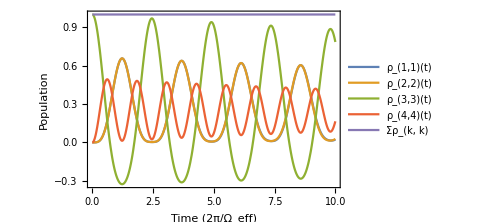

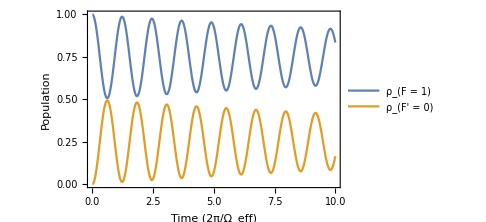

```mathematica
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic]](*,MaxStepFraction->0.001]]*);
Print["Time to run sim: ",time];
labels=rho[[;;dim]];
AppendTo[labels,"Σρ_(k, k)"];
lines=Re[(rho/.soln)[[;;dim]]];
AppendTo[lines,Total[(rho/.soln)[[;;dim]]]];
(*Plot[Evaluate[lines], {t, 0,tmax },PlotRange->All,PlotLegends->labels]*)
Plot[Evaluate[lines/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->labels,FrameLabel->{"Time (2π/Ω_eff)","Population"}]
linesF1=Re[(rho/.soln)[[;;3]]];
linesF0=Re[(rho/.soln)[[4]]];
Plot[Evaluate[{Total[linesF1],linesF0}/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->All,PlotLegends->{"ρ_(F = 1)","ρ_(F' = 0)"},FrameLabel->{"Time (2π/Ω_eff)","Population"}]
```

## ^87 Rb - D1 optical pumping with D2 repump

Optical pumping to the F=1,m=0 ground state. Linear pump light is resonant with F=1->F’=1, and linear repump light is resonant with F=2->F’=2

```mathematica
(*states with n,L,J,F,mF, and angular frequency (energy) in 2π*GHz wrt ground state C.o.M. energy*)

Fglist=Range[Abs[INuc-1/2],INuc+1/2];(*list of ground state hyperfine levels F*)
Fe1list=Range[Abs[INuc-1/2],INuc+1/2];
Fe2list=Range[Abs[INuc-3/2],INuc+3/2];
FivePThreeHalves=Flatten[Table[Table[{5,1,3/2,f,mf},{mf,Range[-f,f]}],{f,Fe2list}(*Range[Abs[INuc-3/2],INuc+3/2]}*)],1];
FivePOneHalf=Flatten[Table[Table[{5,1,1/2,f,mf},{mf,Range[-f,f]}],{f,Fe1list}],1];
FiveSOneHalf=Flatten[Table[Table[{5,0,1/2,f,mf},{mf,Range[-f,f]}],{f,Fglist}],1];
states=Join[FiveSOneHalf,FivePOneHalf,FivePThreeHalves];
{n,L,J,F,mF}=Transpose@states;
"Total number of states:"
dim=Length[states]

(*the energy of each state*)
ω=Table[2π Rb87fGHz[states[[i]][[;;4]]],{i,Range[dim]}];

(*lists of field amplitudes, ang. frequencies, polarization, and angle in rad*)
Clear[Εpump,Εrepump,γD1,γD2,dD1,dD2](*leave symbolic so it's easy to read the equations*);

det =2π*10^-10;(*detuning. must be finite, but can be arbitrarily small... where does the 1/0 come from?*)
Efields={{Εpump,2π(Rb87fGHz[{5,1,1/2,1}]-Rb87fGHz[{5,0,1/2,1}]-det),0,0},{Εrepump,2π(Rb87fGHz[{5,1,3/2,2}]-Rb87fGHz[{5,0,1/2,2}]-det),0,0}};
{Ep,ωp,q,θ}=Transpose@Efields;
dimE=Length[Ep];

(*--things that depend on a pair of state indices j and k--*)
E1FineReduced[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},dD1,{{5,0,1/2},{5,1,3/2}},dD2,_,0];(*get hardcoded D1 or D2 line reduced dipole matrix element.*)

dRotated[m_,n_,p_]:=Module[{j,k},
{j,k}=Sort[{m,n}];(*because the matrix element is real, it is equal to its complex conjugate. Hence, d[m,n,p]=d[n,m,p].*)
Quiet[(Sum[WignerD[{F[[k]],mF[[k]],mFk},θ[[p]]]WignerD[{F[[j]],mFj,mF[[j]]},θ[[p]]]ClebschGordan[{F[[j]],mFj},{1,q[[p]]},{F[[k]],mFk}],{mFk,Range[-F[[k]],F[[k]]]},{mFj,Range[-F[[j]],F[[j]]]}])(-1)^(1+INuc+J[[k]]+F[[j]])√(2F[[j]]+1)SixJSymbol[{J[[j]],INuc,F[[j]]},{F[[k]],1,J[[k]]}]E1FineReduced[j,k]]
]

γE1[j_,k_]:=Switch[Sort[{{n[[j]],L[[j]],J[[j]]},{n[[k]],L[[k]],J[[k]]}}],{{5,0,1/2},{5,1,1/2}},γD1,{{5,0,1/2},{5,1,3/2}},γD2,_,0];(*get hardcoded D1 or D2 line natural linewidth.*)

(*branching factor from an upper state k to j*)
b[{J_,F_,mF_},{JJ_,FF_,mFF_}]:=Quiet[(2F+1)SixJSymbol[{J,INuc,F},{FF,1,JJ}]^2 ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}]^2];

(*pre-evaluate b values*)
Table[Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]=b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}],{j,Range[dim]},{k,Range[j,dim]}];

(*decay from state k to j*)
γ[j_,k_]:=γE1[j,k](Subscript[bb, J[[j]],F[[j]],mF[[j]],J[[k]],F[[k]],mF[[k]]]/Total[Flatten[Table[Subscript[bb, J[[1]],Fg,mFg,J[[k]],F[[k]],mF[[k]]],{Fg,Fglist},{mFg,Range[-Fg,Fg]}],1]]);
(*γ[j_,k_]:=γE1[j,k](b[{J[[j]],F[[j]],mF[[j]]},{J[[k]],F[[k]],mF[[k]]}]/Total[Flatten[Table[Table[b[{J[[1]],Fg,mFg},{J[[k]],F[[k]],mF[[k]]}],{mFg,Range[-Fg,Fg]}],{Fg,Fglist}]]]);*)

Δ[p_,k_,j_]:=ωp[[p]]-(ω[[k]]-ω[[j]]);

(*pre-evaluate γ, d, and Δ values which we can "look up" by index*)
Table[γlookup[j,k]=γ[j,k],{j,Range[dim]},{k,Range[j,dim]}];
Table[dlookup[j,k,p]=dRotated[j,k,p],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];
Table[Δlookup[p,k,j]=Δ[p,k,j],{p,Range[dimE]},{j,Range[dim]},{k,Range[dim]}];

(*terms with detunings of greater order of magnitude (GHz) than this will be dropped*)
drop=OoM[1]+1;(*GHz*)

(*coherence equations to exclude for an approximate but much faster result*)
gExclude=Flatten[Table[{k,j},{j,Range[8]},{k,Range[j+1,8]}],1];(*coherences betweeen  5S1/2 hyperfine states*)
eExclude=Flatten[Table[{k,j},{j,Range[9,30]},{k,Range[j+1,30]}],1];(*coherences betweeen  5P1/2 hyperfine states, 5P3/2 states, and between 5P1/2 and 5P3/2 states*)
exclude=Join[gExclude,eExclude];

Eqs = MEqs[states,Ep,Δlookup,dlookup,γlookup,drop,exclude];(*generate the differential equations*)
"Number of equations"
Eqs//Length
(*"The equations to be solved:"
For[i=1,i<Length[Eqs]+1,i++,
Print[Eqs[[i]]//Expand//TraditionalForm]
]*)
```

Total number of states:

32

Number of equations

269

```mathematica
(*--define numerical constants--*)
dD1=D1MatElem;
dD2=D2MatElem;
γD1=ΓD1*10^-9;
γD2=ΓD2*10^-9;
Εpump=√(2/(c ϵ0)IsatD1SI) /GHz;
Εrepump=100√(2/(c ϵ0)IsatD2SI) /GHz;

(*--setup for the numerical solver--*)

(*the list of populations and coherences we're including, in the same order as in Eqs*)
rho=Join[Table[Subscript[ρ, k,k][t],{k,Range[dim]}],Complement[Flatten[Table[Subscript[ρ, k,l][t],{l,1,dim},{k,l+1,dim}],1],Array[Subscript[ρ, exclude[[#,1]],exclude[[#,2]]][t]&,Length[exclude]]]];
rho0=Array[0&,Length[rho]];
initialStates=Range[3];
rho0[[initialStates]]=1/(initialStates//Length);
Ωpump=Εpump dRotated[1,9,1]/ℏ;
Ωrepump=Εpump dRotated[4,21,1]/ℏ;
Ωeff=Abs[Ωpump] ;
Print["Pump Rabi frequency = 2π*",Abs[Ωpump]/(2π) GHz/MHz," MHz"]
Print["Repump Rabi frequency = 2π*",Abs[Ωrepump]/(2π) GHz/MHz," MHz"]
Print["Ω_pump/γD1 = ",Abs[Ωpump]/γD1]
Print["Ω_repump/γD2 = ",Abs[Ωrepump]/γD2]
tmax=15*2π/Ωeff;
```

Pump Rabi frequency = 2π*1.44304 MHz

Repump Rabi frequency = 2π*2.88298 MHz

Ω_pump/γD1 = 0.251104

Ω_repump/γD2 = 0.475277

Time to run sim: 30.5625

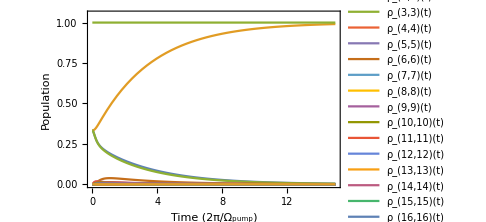

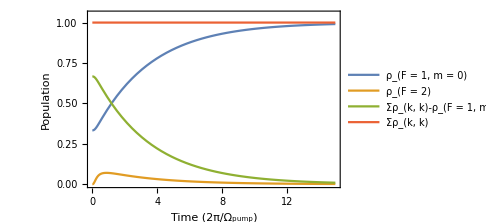

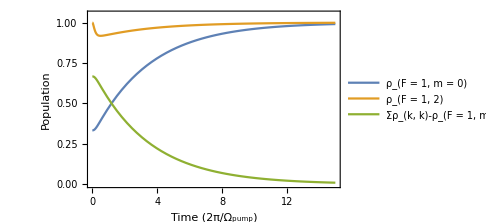

```mathematica
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax},Method->Automatic]](*,MaxStepFraction->0.001]]*);
Print["Time to run sim: ",time];
labels=rho[[;;dim]];
AppendTo[labels,"Σρ_(k, k)"];
lines=Re[(rho/.soln)[[;;dim]]];
AppendTo[lines,Total[(rho/.soln)[[;;dim]]]];
(*Plot[Evaluate[lines], {t, 0,tmax },PlotRange->All,PlotLegends->labels]*)
Plot[Evaluate[lines/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->{{0,tmax Ωeff/(2π)},{0,1.05}},PlotLegends->labels,FrameLabel->{"Time (2π/Ω_pump)","Population"}]
Plot[Evaluate[{lines[[2]],Total[lines[[4;;8]]],1-lines[[2]],lines[[-1]]}/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotRange->{{0,tmax Ωeff/(2π)},{0,1.05}},PlotLegends->{"ρ_(F = 1, m = 0)","ρ_(F = 2)","Σρ_(k, k)-ρ_(F = 1, m = 0)","Σρ_(k, k)"},FrameLabel->{"Time (2π/Ω_pump)","Population"}]
Plot[Evaluate[{lines[[2]],Total[lines[[1;;8]]],1-lines[[2]](*,lines[[-1]]*)}/.t->τ (2π)/Ωeff], {τ, 0,tmax Ωeff/(2π)},PlotLegends->{"ρ_(F = 1, m = 0)","ρ_(F = 1, 2)","Σρ_(k, k)-ρ_(F = 1, m = 0)","Σρ_(k, k)"},FrameLabel->{"Time (2π/Ω_pump)","Population"},PlotRange->{{0,tmax Ωeff/(2π)},{0,1.05}}]
```

Same plots as above, but time in microseconds.

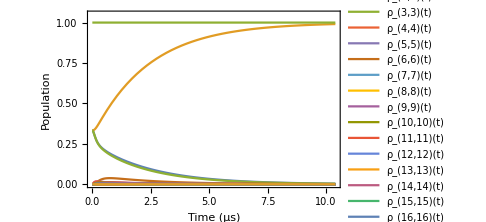

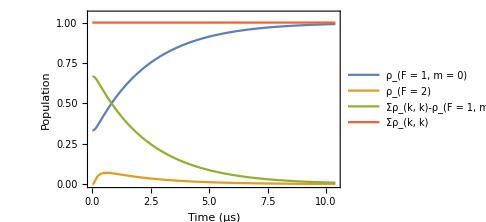

```mathematica
Plot[Evaluate[lines/.t->τ 1000], {τ, 0,tmax/1000},PlotRange->{{0,tmax/1000},{0,1.05}},PlotLegends->labels,FrameLabel->{"Time (μs)","Population"}]
Plot[Evaluate[{lines[[2]],Total[lines[[4;;8]]],1-lines[[2]],lines[[-1]]}/.t->τ 1000], {τ, 0,tmax/1000},PlotRange->{{0,tmax/1000},{0,1.05}},PlotLegends->{"ρ_(F = 1, m = 0)","ρ_(F = 2)","Σρ_(k, k)-ρ_(F = 1, m = 0)","Σρ_(k, k)"},FrameLabel->{"Time (μs)","Population"}]
```

## Two-level atom test

First, leave everything symbolic to see if the correct equation is generated (check with eq. 10.28 of Mark’s notes). For this symbolic test I have set ℏ=1 below. 

Upon inspection there are some differences, particularly in the coherence equation. I think this is because the equation below does not make the ρ̃ substitution.

```mathematica
(*group states by {quantum numbers,ω}, ascending in energy*)
Clear[t]
(*simplifies debugging*)
states={{gg,0},{ee,ωa}};
{level,energies}=Transpose@states;
(*lists of field amplitudes and ang. freq*)
Efields={{E1,ω}};
{Ep,ωp} = Transpose@Efields;
dimE=Length[Ep];
(*things that depend on a pair of state indices j and k:*)
d[j_,k_]:=(1-δ[j,k])If[k<j,deg ,dge];(*trivial*)
γ[j_,k_]:= (1-δ[j,k])γeg;
Δ[p_,k_,j_]:=ωp[[p]]-(energies[[k]]-energies[[j]]);
(*trivial, 2 is upper state*)
(*build the equations for each element of the density matrix.
redundant equations,i.e. complex conjugates of the off-diagonals are omitted.*)
dim = Length[states];
Eqs={};
For[l=1,l<dim+1,l++,
For[k=l,k<dim+1,k++,
RHS=
δ[k,l](-Sum[γ[j,k]Subscript[ρ, k,k][t],{j,Range[1,k-1]}]+Sum[γ[k,j]Subscript[ρ, j,j][t],{j,Range[k+1,dim]}]
-(ⅈ/2)(Sum[-Ep[[p]]d[k,j]Subscript[ρ, k,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,k]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,k,j]t],{p,Range[dimE]},{j,Range[1,k-1]}]
+Sum[Ep[[p]]d[j,k]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,k]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,k][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k+1,dim]}]))
+(1/2)(1-δ[k,l])(-(Sum[γ[j,k],{j,Range[1,k-1]}]+Sum[γ[j,l],{j,Range[1,l-1]}])Subscript[ρ, k,l][t]
+Sum[γ[k,j]Subscript[ρ, j,l][t]δ[j,l],{j,Range[k+1,dim]}]+Sum[γ[l,j]Subscript[ρ, k,j][t]δ[j,l],{j,Range[l+1,dim]}]
-ⅈ(Sum[-Ep[[p]]d[k,j]Subscript[ρ, l,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,l]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,l,j]t],{p,Range[dimE]},{j,Range[1,l-1]}]
+Sum[Ep[[p]](d[j,l]Subscript[ρ, k,j][t]Exp[-ⅈ Δ[p,j,l]t]-d[k,j]Subscript[ρ, j,l][t]Exp[-ⅈ Δ[p,k,j]t]),{p,Range[dimE]},{j,Range[l,k-1]}]
+Sum[Ep[[p]]d[j,l]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,l]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,l][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k,dim]}]))//FullSimplify;
AppendTo[Eqs,D[Subscript[ρ, k,l][t],t]==RHS];
Print[TraditionalForm[D[Subscript[ρ, k,l][t],t]==RHS//TrigToExp]];
]
]
```

ρ_(1,1)'(t)==-1/2 ⅈ deg E1 ⅇ^(-ⅈ t (ω-ωa)) Conjugate[ρ_(2,1)(t)]+1/2 ⅈ dge Conjugate[E1] ρ_(2,1)(t) ⅇ^(ⅈ t (ω-ωa))+γeg ρ_(2,2)(t)

ρ_(2,1)'(t)==-1/2 ⅈ deg E1 ⅇ^(-ⅈ t (ω-ωa)) Conjugate[ρ_(2,2)(t)]+1/2 ⅈ deg E1 ρ_(1,1)(t) ⅇ^(-ⅈ t (ω-ωa))-1/2 γeg ρ_(2,1)(t)

ρ_(2,2)'(t)==1/2 ⅈ deg E1 ⅇ^(-ⅈ t (ω-ωa)) Conjugate[ρ_(2,1)(t)]-1/2 ⅈ dge Conjugate[E1] ρ_(2,1)(t) ⅇ^(ⅈ t (ω-ωa))-γeg ρ_(2,2)(t)

Test of simulated Rabi oscillations and relaxation.

```mathematica
states={{gg,0},{ee,1}};
{level,energies}=Transpose@states;
(*lists of field amplitudes and ang. freq*)
Efields={{1,1}};
{Ep,ωp} = Transpose@Efields;
dimE=Length[Ep];
(*things that depend on a pair of state indices j and k:*)
d[j_,k_]:=(1-δ[j,k]);(*trivial*)
γ[j_,k_]:=(1-δ[j,k])0.1;
Δ[p_,k_,j_]:=ωp[[p]]-(energies[[k]]-energies[[j]]);
Clear[Eqs];
Eqs={};
For[l=1,l<dim+1,l++,
For[k=l,k<dim+1,k++,
RHS=
δ[k,l](-Sum[γ[j,k]Subscript[ρ, k,k][t],{j,Range[1,k-1]}]+Sum[γ[k,j]Subscript[ρ, j,j][t],{j,Range[k+1,dim]}]
-ⅈ/2(Sum[-Ep[[p]]d[k,j]Subscript[ρ, k,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,k]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,k,j]t],{p,Range[dimE]},{j,Range[1,k-1]}]
+Sum[Ep[[p]]d[j,k]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,k]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,k][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k+1,dim]}]))
+1/2(1-δ[k,l])(-(Sum[γ[j,k],{j,Range[1,k-1]}]+Sum[γ[j,l],{j,Range[1,l-1]}])Subscript[ρ, k,l][t]
+Sum[γ[k,j]Subscript[ρ, j,l][t]δ[j,l],{j,Range[k+1,dim]}]+Sum[γ[l,j]Subscript[ρ, k,j][t]δ[j,l],{j,Range[l+1,dim]}]
-ⅈ(Sum[-Ep[[p]]d[k,j]Subscript[ρ, l,j][t]*Exp[-ⅈ Δ[p,k,j]t]+Ep[[p]]*d[j,l]Subscript[ρ, k,j][t]Exp[ⅈ Δ[p,l,j]t],{p,Range[dimE]},{j,Range[1,l-1]}]
+Sum[Ep[[p]](d[j,l]Subscript[ρ, k,j][t]Exp[-ⅈ Δ[p,j,l]t]-d[k,j]Subscript[ρ, j,l][t]Exp[-ⅈ Δ[p,k,j]t]),{p,Range[dimE]},{j,Range[l,k-1]}]
+Sum[Ep[[p]]d[j,l]Subscript[ρ, j,k][t]*Exp[-ⅈ Δ[p,j,l]t]-Ep[[p]]*d[k,j]Subscript[ρ, j,l][t]Exp[ⅈ Δ[p,j,k]t],{p,Range[dimE]},{j,Range[k,dim]}]))//FullSimplify;
AppendTo[Eqs,D[Subscript[ρ, k,l][t],t]==RHS];
Print[TraditionalForm[D[Subscript[ρ, k,l][t],t]==RHS]];
]
]
tmax=10/(Ep[[1]]d[1,2]);
rho={Subscript[ρ, 1,1][t],Subscript[ρ, 2,1][t],Subscript[ρ, 2,2][t]};
rho0={1,0,0};
icEqs=Array[(rho/.t-> 0)[[#]]==rho0[[#]]&,Length[rho]];
{time,soln}= Timing[First@NDSolve[Flatten@Join[Eqs,icEqs], rho, {t,0,tmax}]];
Print["Time to run sim: ",time];
```

ρ_(1,1)'(t)==-ⅈ Re(ρ_(2,1)(t))+ⅈ ρ_(2,1)(t)+0.1 ρ_(2,2)(t)

ρ_(2,1)'(t)==(0.-0.5 ⅈ) Conjugate[ρ_(2,2)(t)]+(0.+0.5 ⅈ) ρ_(1,1)(t)-0.05 ρ_(2,1)(t)

ρ_(2,2)'(t)==-0.1 ρ_(2,2)(t)+ⅈ (Re(ρ_(2,1)(t))-ρ_(2,1)(t))

Time to run sim: 0.

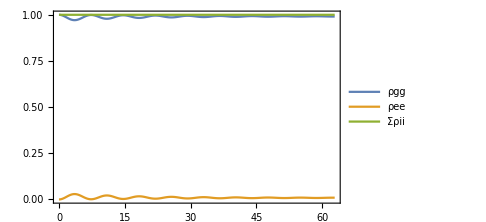

```mathematica
plt ={};
labels={"ρgg","ρee","Σρii"};
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,soln[[i,2]]]
];
populations={1,3};
AppendTo[plt,Total[soln[[populations,2]]]];
AppendTo[populations,-1];
Plot[Evaluate[plt[[populations]]], {t, 0, tmax},PlotRange->All,PlotLegends->labels]
```